```mathematica
SetDirectory["/home/leonard/Documents/ProjectData/PhysicalDistance/spinChain/"];
foldPref="N=15_M=5_defec=0.01";
ind1=Import["./N=15_M=5_defec=0.01/ind.dat","Table"]//Flatten;
ind2=Import["./N=15_M=5_defec=0.5/ind.dat","Table"]//Flatten;
eff1=Import["./N=15_M=5_defec=0.01/eff.dat","Table"]//Flatten;
eff2=Import["./N=15_M=5_defec=0.5/eff.dat","Table"]//Flatten;
```

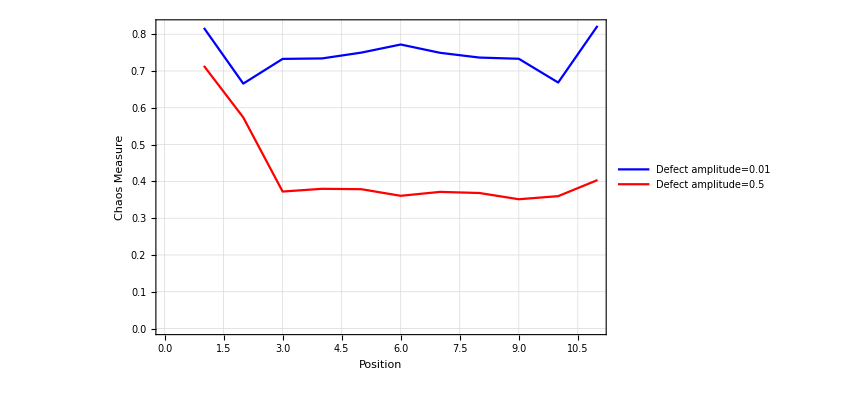

```mathematica
ListLinePlot[{ind1,ind2},{PlotTheme->"Detailed",PlotLegends->Placed[{"Defect amplitude=0.01","Defect amplitude=0.5"},{Center,Bottom}],FrameLabel->{"Position","Chaos Measure"},PlotStyle->{Blue,Red},FrameStyle->15}]
```

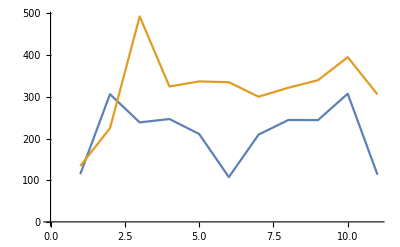

```mathematica
ListLinePlot[{eff1,eff2}]
```

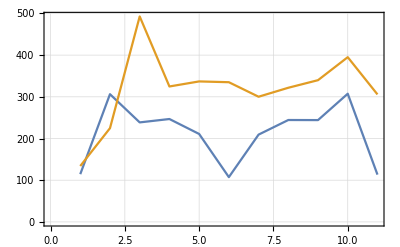

```mathematica
ListLinePlot[{eff1,eff2},PlotTheme->"Detailed"]
```

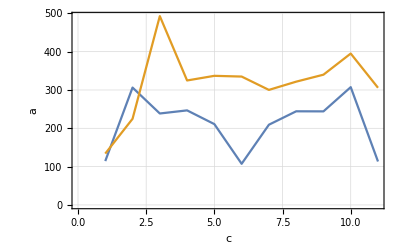

```mathematica
Show[%235,FrameLabel->{{HoldForm[a],HoldForm[b]},{HoldForm[c],HoldForm[d]}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
esp=Import["/home/leonard/Documents/ProjectData/PhysicalDistance/spinChain/N=15_M=5_defec=0.01/EspacingData.txt","Table"];
esp1=Import["/home/leonard/Documents/ProjectData/PhysicalDistance/spinChain/N=15_M=5_defec=0.5/EspacingData.txt","Table"];
```

```mathematica
pois=Transpose[{esp⟦;;,1⟧,esp⟦;;,4⟧}];
wig=Transpose[{esp⟦;;,1⟧,esp⟦;;,3⟧}];
es1=Transpose[{esp⟦;;,1⟧,esp⟦;;,2⟧}];
es2=Transpose[{esp1⟦;;,1⟧,esp1⟦;;,2⟧}];
```

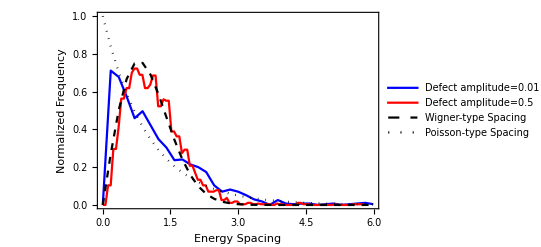

```mathematica
ListLinePlot[Select[#,#⟦1⟧≤6.&]&/@{es1,es2,wig,pois},{PlotRange->All,PlotStyle->{Blue,Red,Directive[Black,Dashed],Directive[Black,Dotted]},PlotLegends->Placed[{"Defect amplitude=0.01","Defect amplitude=0.5","Wigner-type Spacing","Poisson-type Spacing"},{0.7,0.75}],Frame->True,FrameStyle->13,
FrameLabel->{"Energy Spacing","Normalized Frequency"}
}]
```

```mathematica
Export["/home/leonard/Documents/Projects/PhysicalDistance/Paper/figs/fig7.png",%84]
```

/home/leonard/Documents/Projects/PhysicalDistance/Paper/figs/fig7.png